# FileAdapterGSDGSH test

```mathematica
<<NounouW`
```

HokahokaW`
(origin)[https://ktakagaki@github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  13ddb7cc898ce8f990bcd7062e894fd2ef4ee0a2
newest file:  Wed 1 Oct 2014 17:17:02

NounouW`
(origin)[https://ktakagaki@github.com/ktakagaki/NounouW.git]
current Git HEAD:  7efb7dbf0cba085c609829b3770a97b2b4a4e8c8
newest file:  Wed 1 Oct 2014 17:24:43

<<Set JLink` java stack size to 6144Mb>>

```mathematica
ShowJavaConsole[];
```

```mathematica
testDataFile = "C:\\prog\\_gh\\_kt\\nounou\\src\\test\\resources\\_testFiles\\Micam\\mag130712008A_3.gsd";
```

```mathematica
reader=JavaNew["nounou.NNDataReader"]
```

«JavaObject[nounou.NNDataReader]»

```mathematica
reader@load[testDataFile]
```

{«JavaObject[nounou.data.io.XHeaderGSD]»,«JavaObject[nounou.data.io.XDataGSD]»,«JavaObject[nounou.data.io.XDataGSDAux]»,«JavaObject[nounou.data.XLayoutSquare]»}

```mathematica
$NNReader@toStringChain[]
```

DataReader LOADED DATA SUMMARY
================================
DataReader( data ch:7360, dataAux ch:2, mask: XMask: 0 _masks, events: 0)

     [header  ] XHeader: 26 entries
     [dataORI ] XDataFilterHolder: XData: 7360 ch, 1 seg, lengths=Vector(1024), fs=500.0)     
          \ XDataFilterDecimate: off (factor=1)     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterMinMaxAbs: halfWindow=25
                    \ XDataFilterFIR: kernel null (off)
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: halfWindow=25
     [dataAux ] XDataFilterHolder: XData: 2 ch, 1 seg, lengths=Vector(1024), fs=500.0)
     [mask    ] XMask: 0 _masks
     [events  ] XEventsNull
     [spikes  ] XSpikesNull

```mathematica
$NNReader@dataFIR[]@segmentLengths[]@toString[]
```

Vector(1024)

```mathematica
$NNReader@dataDecimate[]@segmentLengths[]@toString[]
```

Vector(1024)

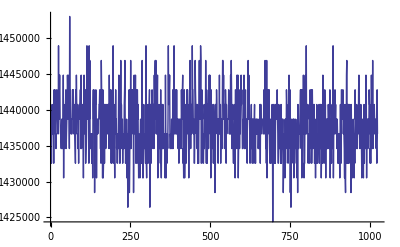

```mathematica
ListLinePlot[$NNReader@dataFIR[]@readTraceAbsA[100, NN`frameRangeAll[]]]
```

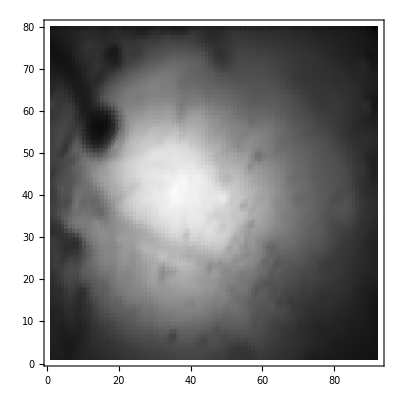

```mathematica
ListDensityPlot[Partition[$NNReader@dataFIR[]@readFrameA[0,0],92],ColorFunction->GrayLevel]
```

```mathematica
$NNReader@dataORI[]@heldDataU$eq[]
```

Java::argx0: Method named "heldDataU$eq" defined in class "nounou.data.filters.XDataFilterHolder" does not take zero arguments.

$Failed

```mathematica
Methods[$NNReader@dataORI[]]
```